```mathematica
Integrate[E^(-2/3/e)/e^(3/2)*√Pi,{e,0,∞}]
```

√(3/2) π

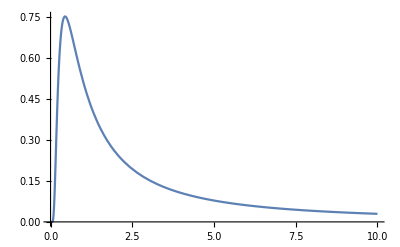

```mathematica
Plot[E^(-2/3/e)/e^(3/2),{e,0,10}]
```

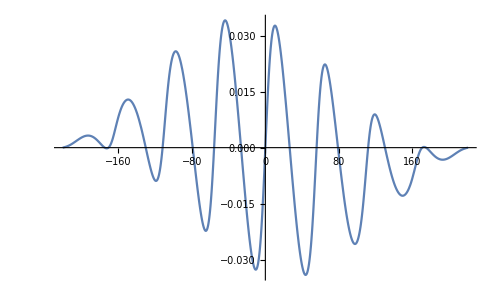

```mathematica
w=0.057;func=D[Cos[(w t)/8]^2*1.325/(√5)*√(4*Sin[w t]^2+Cos[w t]^2),t];Plot[func,{t,-2*110.23,2*110.23}]
```

```mathematica
func
```

(0.101327 Cos[0.007125 t]^2 Cos[0.057 t] Sin[0.057 t])/(√(Cos[0.057 t]^2+4 Sin[0.057 t]^2))-0.00844395 Cos[0.007125 t] Sin[0.007125 t] √(Cos[0.057 t]^2+4 Sin[0.057 t]^2)

```mathematica
D[func,t]
```

-(0.017327 Cos[0.007125 t]^2 Cos[0.057 t]^2 Sin[0.057 t]^2)/((Cos[0.057 t]^2+4 Sin[0.057 t]^2)^(3/2))+(0.00577566 Cos[0.007125 t]^2 Cos[0.057 t]^2)/(√(Cos[0.057 t]^2+4 Sin[0.057 t]^2))-(0.00288783 Cos[0.007125 t] Cos[0.057 t] Sin[0.007125 t] Sin[0.057 t])/(√(Cos[0.057 t]^2+4 Sin[0.057 t]^2))-(0.00577566 Cos[0.007125 t]^2 Sin[0.057 t]^2)/(√(Cos[0.057 t]^2+4 Sin[0.057 t]^2))-0.0000601632 Cos[0.007125 t]^2 √(Cos[0.057 t]^2+4 Sin[0.057 t]^2)+0.0000601632 Sin[0.007125 t]^2 √(Cos[0.057 t]^2+4 Sin[0.057 t]^2)

```mathematica
NSolve[D[func,t]==0,t]
```

{}

```mathematica
func/.t->43.8
```

-0.0341017

```mathematica
Integrate[(e+1)^(-3/2),{e,0,∞}]
```

2

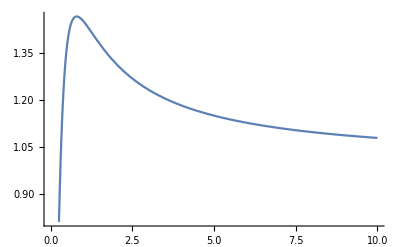

```mathematica
Plot[E^(-2/3/e)/e^(3/2)(e+1)^(3/2),{e,0,10}]
```

```mathematica
Solve[D[E^(-2/3/e)/e^(3/2)(e+1)^(3/2),e]==0,e]
```

{{e→-1},{e→4/5}}

```mathematica
E^(-2/3/e)/e^(3/2)(e+1)^(3/2)/.Solve[D[E^(-2/3/e)/e^(3/2)(e+1)^(3/2),e]==0,e]//N
```

{0.,1.46677}

```mathematica
E^(-2/3/e)/e^(3/2)(e+1)^(3/2)/.e->0.1//N
```

0.0464293